# Deriving the empirical correlation function and fitting a curve to it

## Translating from “Towards a unified descriptive theory for spatial ecology” (who only provide a PDF of their Mathematica notebook!)

M Scott & M Osmond
2016 January 21

Define the spatial extent of the area of interest (e.g., Barro Colorado Island)

```mathematica
{Lx,Ly}={1000,500}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=100;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Make up the data (because the authors suck at making it available)

```mathematica
numplots=1000;(*number of plots/datapoints*)
data=Table[{{RandomVariate[NormalDistribution[Lx/2,Lx/10]],RandomVariate[NormalDistribution[Ly/2,Ly/10]]},RandomInteger[{1,3}],RandomInteger[10]},{i,1,numplots}];
(*(x,y) locations of each plot, species code of each plot,abundance of that species in each plot*)
```

Get each variable of interest from data table

```mathematica
gx=Table[Transpose[data][[1]][[i,1]],{i,1,numplots}]; (*x coordinates of all plots*)
gy=Table[Transpose[data][[1]][[i,2]],{i,1,numplots}]; (*y coordinates of all plots*)
sp=Transpose[data][[2]];(*species code for each plot*)
ab=Transpose[data][[3]];(*species abundance at each plot*)
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1](*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1](*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie (*number of plots with each species in each bin*)
SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) (*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]-(Mean[SabA[i]] Mean[SabA[j]])//N;(*covariance in number of plots with species across bins, note that the covariance is taken over all species*)
allcov=ParallelTable[Map[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covaraiance in number of plots with species at each distance*)
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

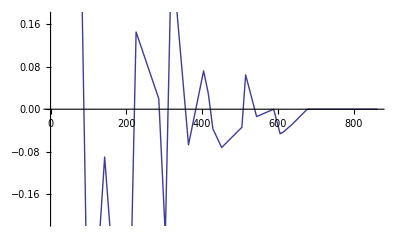

```mathematica
ListPlot[empPCF,Joined->True]
```

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,10^9},{ρ,0.1}},r];(*fit the function, with some parameter guesses*)
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

AdjustedRSquared | -35.4479
AIC | 88.6684
BIC | 92.665
RSquared | -32.8445

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 1.×10^9 | 3.53682×10^30 | 2.8274×10^-22 | 1
ρ | 0.1 | 3.41672×10^20 | 2.92678×10^-22 | 1

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 1.×10^9 | 3.53682×10^30 | {-7.27003×10^30,7.27003×10^30}
ρ | 0.1 | 3.41672×10^20 | {-7.02318×10^20,7.02318×10^20}

Plot fitted curve with data points

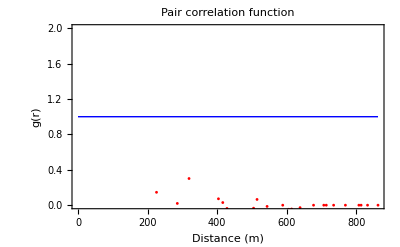

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},{0,All}},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False
]
```

Plot fitted curve with confidence bands

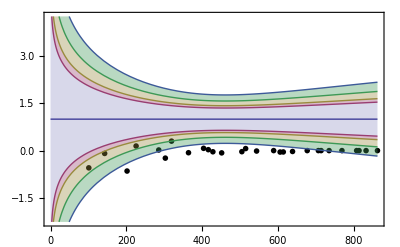

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},{0,All}},
Frame->{True,True,False,False}]
```